```mathematica
(* The Base directory when working on the lab computer *)
dropBoxOn=FileNameJoin[{"Dropbox","00School","research"}];
labComp=FileNameJoin[{"C:","Users","karl",dropBoxOn}];
homeComp=FileNameJoin[{"/","home","karl",dropBoxOn}];
(* The folder that contains the different data runs to analyze, this folder contains subfolders with 
individual runs.*)
dataFolder=FileNameJoin[{labComp}]
SetDirectory[dataFolder];
(* Make a list of directories to easily select the folder you would like to work with.*)
directories=Select[FileNames["*","",1],DirectoryQ];
For[i=1,i<=Length[directories],i++,
Print[i -> directories[[i]]];]
```

C:\Users\karl\Dropbox\00School\research

1→3_15_17_AimingFor5e12

2→data

3→firstRun2017

4→labBook

5→legacy

6→machineShopOrders

7→mathematicaCode

8→operationManuals

9→papers

10→polarization_4-4-17

11→polarization_4-6-17

12→pumpLaserFindingCircular_3-29_17

13→RbControlPiPrograms

14→rbsim

15→requisitions

16→wavemeterNoRb

17→wavemeterReliability_3-30-17

{FDayScan2017-04-06_172650RotationAnalysis.dat,FDayScan2017-04-06_172957RotationAnalysis.dat,FDayScan2017-04-06_173301RotationAnalysis.dat,FDayScan2017-04-06_174103RotationAnalysis.dat,FDayScan2017-04-06_174407RotationAnalysis.dat,FDayScan2017-04-06_174711RotationAnalysis.dat,FDayScan2017-04-06_175046RotationAnalysis.dat,FDayScan2017-04-06_175355RotationAnalysis.dat,FDayScan2017-04-06_175658RotationAnalysis.dat,FDayScan2017-04-06_180603RotationAnalysis.dat,FDayScan2017-04-06_180906RotationAnalysis.dat,FDayScan2017-04-06_181210RotationAnalysis.dat,FDayScan2017-04-06_181555RotationAnalysis.dat,FDayScan2017-04-06_181858RotationAnalysis.dat,FDayScan2017-04-06_182202RotationAnalysis.dat,FDayScan2017-04-06_182608RotationAnalysis.dat,FDayScan2017-04-06_182912RotationAnalysis.dat,FDayScan2017-04-06_183216RotationAnalysis.dat,FDayScan2017-04-06_183615RotationAnalysis.dat,FDayScan2017-04-06_183918RotationAnalysis.dat,FDayScan2017-04-06_184222RotationAnalysis.dat,FDayScan2017-04-06_184554RotationAnalysis.dat,FDayScan2017-04-06_184723RotationAnalysis.dat,FDayScan2017-04-06_184852RotationAnalysis.dat}

{RbAbs2017-04-06_171537.dat,RbAbs2017-04-06_172031.dat,RbAbs2017-04-06_172953.dat}

RbAbs2017-04-06_172031.dat

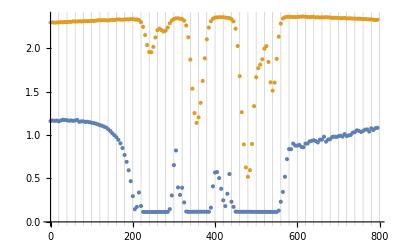

Import::nffil: File not found during Import.

$Failed

Import::nffil: File not found during Import.

$Failed

```mathematica
(* set rootFolder to the folder name containing the RbPolarization Files *)
rootFolder=FileNameJoin[{dataFolder,directories[[11]]}];
SetDirectory[rootFolder];
(* Obtain the filename of the absorption data *)
scanFiles=FileNames["FDayScan"~~RegularExpression[".{25,25}"]~~"Analysis.dat"]
noPump=scanFiles[[1]];

(*** In the future, the following will be removed as we will no longer take an absorption
profile in order to calculate the detunings. ***) 
absFileNames=FileNames["RbAbs*.dat"]
absFileName=absFileNames[[2]]
(*Import the faraday rotation data*)
rotationAnalysisDataFile=Import[FileNameJoin[{rootFolder,scanFiles[[2]]}],"tsv"];
(*Import the absorption data*)
rbAbsorption=Import[FileNameJoin[{Directory[],absFileName}],"tsv"];
(* Drop the information from the file that isn't needed *)
rbAbsorptionRef=Drop[Take[rbAbsorption,{8,-2},{1,6}],None,{2,5}];
rbAbsorptionPro=Drop[Take[rbAbsorption,{8,-2},{1,4}],None,{2,3}];
(* Plot the data so the user can see the first minimum *)
ListPlot[{rbAbsorptionPro,rbAbsorptionRef},Ticks-> {Range[0,1023,20],Automatic},GridLines->{Range[0,1023,20],None}]

(*** Instead, it will be replaced with this code, which reads in a .tsv with the detunings used. ***)
wavemeterDetunings1=Transpose[Import["NegativeDetunings.tsv","tsv"]][[1]]
wavemeterDetunings2=Transpose[Import["PositiveDetunings.tsv","tsv"]][[1]]
```

{{315,4.576},{445,1.84},{560,-1.372},{610,-3.072}}

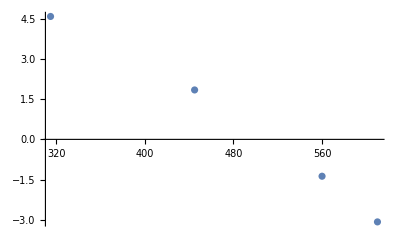

65.3

64.5

105.52-0.394071 x+0.759312 x^2

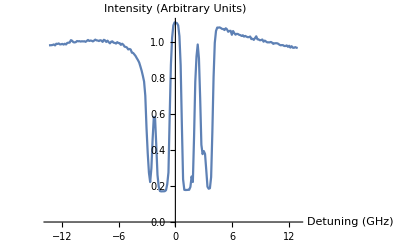

{{794.997,-60.9074},{795.,-61.2031},{795.002,-61.285},{795.005,-61.3259},{795.007,-61.443},{795.01,-61.7066},{795.012,-61.6429},{795.015,-61.6414},{795.018,-61.7476},{795.02,-61.8362},{795.023,-61.9329},{795.026,-61.8587},{795.029,-61.8598},{795.032,-61.8672},{795.035,-61.9148},{795.039,-61.9417},{795.042,-61.9923},{795.045,-64.523},{795.048,-70.1589},{795.051,-70.3323},{795.055,-70.2238}}

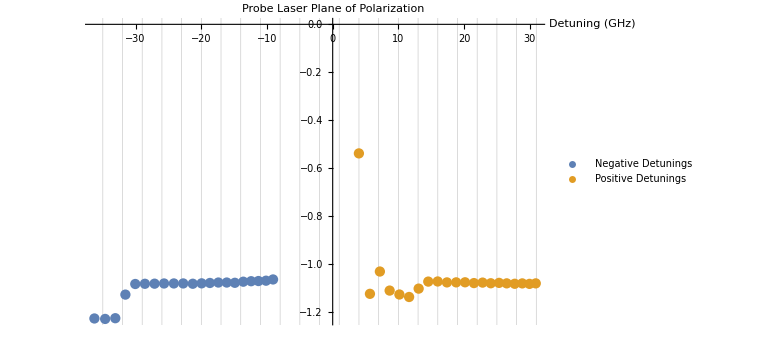

```mathematica
(* User inputs a value close to the first minimum *)
{transistionLetter,aoutValue}={"D",310};
CtoDDiff=110;
BtoCDiff=135;
AtoBDiff=72;
dt=4.576;
ct=1.84;
bt=-1.372;
at=-3.072;
transGHz={4.576,1.84,-1.372,-3.072};
aoutSteps={CtoDDiff,BtoCDiff,AtoBDiff};


(* Find the closest data point to the value chosen by the user*)
s=Nearest[Take[rbAbsorptionRef,All,1],aoutValue];
(* Convert this data point to a position in the list *)
startPos=Position[Take[rbAbsorptionRef,All,1],s[[1]]][[1]][[1]];
(* Use the position in the list to find the first absorption peak's value *)
scanStepSize=-(rbAbsorptionRef[[startPos]]-rbAbsorptionRef[[startPos+1]])[[1]];
posLower=startPos-3;
posUpper=startPos+1;
transAout={0,0,0,0};
i=0;

If[transistionLetter=="D",j=1,If[transistionLetter=="C",j=2,If[transistionLetter=="B",j=3,If[transistionLetter=="A",j=4,j=5]]]];
(* Cycle through and find the remaining transisition "peaks" *)
While[And[posLower>1,j<5],
peak=Min[Take[rbAbsorptionRef,{posLower,posUpper},All]];
(* Use the value of the first absorption peak to find its position in the list *)
aoutPos=Position[rbAbsorptionRef,peak][[1]][[1]];
(* Use the position in the list to get the Aout value located there *)
transAout[[j]]=rbAbsorptionRef[[aoutPos]][[1]];
(* Because the profile is consistent, we can guess at where the next min. will be*)
If[j<4,aoutPrev=transAout[[j]];aoutStep=aoutSteps[[j]];aoutNextApprox=aoutPrev+aoutStep;
s=Nearest[Take[rbAbsorptionRef,All,1],aoutNextApprox];
posUpper=aoutPos+Floor[aoutStep/scanStepSize]+1*Floor[20/scanStepSize];
posLower=aoutPos+Floor[aoutStep/scanStepSize]-1*Floor[20/scanStepSize];
];
j++;
]
(* Remove the transistions that we don't have from the list so that we can estimate a linear 
function relating the data points that we do have *)
aoutConvData=Dataset[Transpose[{transAout,transGHz}]];
aoutConvData=aoutConvData[Select[Abs[#[[1]]]>0&]];
aoutConvData=Normal[aoutConvData]

(* Make a linear fit on the data to obtain an AOUT->GHz Conversion *)
ListPlot[aoutConvData,PlotRange->All]
lm2=LinearModelFit[aoutConvData,x,x];
aoutConv=lm2["BestFitParameters"][[2]];
aoutIntercept=lm2["BestFitParameters"][[1]];
rotationAnalysisData=rotationAnalysisDataFile;

(* Retrieves the recorded voltages of the magnets *)
v1=rotationAnalysisData[[11]][[2]]
v2=rotationAnalysisData[[12]][[2]]
(* The coefficients for the polynomial describing the magnetic field of magnet 1 [(c)oefficient of magent (1)]  based on the current.
Assumes x is measured in cm *)
c1x2=.085;
c1x1=-1.907;
c1x0=17.24;
c2x2=0.153;
c2x1=1.866;
c2x0=15.594;

(* The coefficients for the linear relationship between the current and the voltage of the magnets *)
c1v2iSlope=.0504;
c1v2iInt=-.0113;
c2v2iSlope=.0488;
c2v2iInt=-.0069;

(* Calculate the current in each of the magnets based on the voltage *)
i1=v1*c1v2iSlope+c1v2iInt;
i2=v2*c2v2iSlope+c2v2iInt;

(*Creates a function for obtaining the magnetic field at a given position based on the currents
in the magnets *)
getBEq[i1_,i2_]:=((c1x2 )i1 +(c2x2)i2) x^2 +((c1x1 )i1 +(c2x1)i2) x +((c1x0 )i1 +(c2x0)i2)  ;
getBEq[i1,i2]
BdotL=Integrate[getBEq[i1,i2],{x,0,2.794}] /100/10000;(* Divide by 100 to convert to Gauss*meters, Divide by 10000 to convert to Tesla*meters*)


{aoutAbs,iPro}=Transpose[rbAbsorptionPro];
{aoutAbs,iRef}=Transpose[rbAbsorptionRef];
{detuneAbs,iPro}={aoutAbs*aoutConv+aoutIntercept,iPro};
{detuneAbs,iRef}={detuneAbs,iRef};
rbAbsPro=Transpose[{detuneAbs,iPro}];
rbAbsRef=Transpose[{detuneAbs,iRef}];

(* Remove all data points except the tails (where the absorption doesn't happen) *)
rbAbsProDataset=Dataset[rbAbsPro];
rbAbsProTails=rbAbsProDataset[Select[Abs[#[[1]]]>7&]];
rbAbsProTails=Normal[rbAbsProTails];

(* Make a linear fit on the tails*)
tailsFit=LinearModelFit[rbAbsProTails,x,x];
{detuning,intensity}=Transpose[rbAbsPro];
(* Normalize the intensity with the linear fit *)
For[k=1,k<=Length[detuning],k++,
intensity[[k]]=intensity[[k]]/(tailsFit[detuning[[k]]]);
]
(* Plot the (normalized) absorption profile *)
ListPlot[Transpose[{detuning,intensity}],PlotRange-> {All,All},Joined->True,AxesLabel->{"Detuning (GHz)","Intensity (Arbitrary Units)"},LabelStyle->14]

rotationAnalysisData=Import[FileNameJoin[{rootFolder,scanFiles[[2]]}],"tsv"];
rotationAnalysisData=Drop[Take[rotationAnalysisData,{14,-1},{2,10}],None,{2,8}];
Print[rotationAnalysisData]
{aout,θDeg}=Transpose[rotationAnalysisData];
{detune,θRad}={aout*aoutConv+aoutIntercept,θDeg*Pi/180};
rotationAnalysisData =Transpose[{wavemeterDetunings1,θRad}];
negativeDetunings=rotationAnalysisData;

rotationAnalysisData=Import[FileNameJoin[{rootFolder,scanFiles[[3]]}],"tsv"];
rotationAnalysisData=Drop[Take[rotationAnalysisData,{14,-1},{2,10}],None,{2,8}];
{aout,θDeg}=Transpose[rotationAnalysisData];
{detune,θRad}={aout*aoutConv+aoutIntercept,θDeg*Pi/180};
rotationAnalysisData =Transpose[{wavemeterDetunings2,θRad}];
positiveDetunings=rotationAnalysisData;
allDetuningsPlot=ListPlot[{Legended[negativeDetunings,"Negative Detunings"],Legended[positiveDetunings,"Positive Detunings"]},PlotRange->All,LabelStyle->14,AxesLabel->{"Detuning (GHz)","Probe Laser\nPlane of Polarization"},ImageSize->Large,GridLines->{Range[-35,35,3],None}]
```

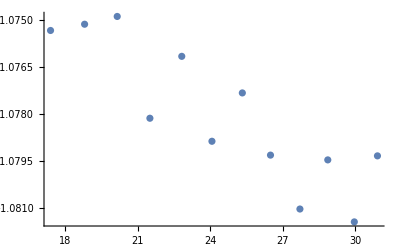

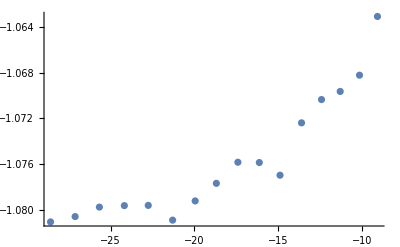

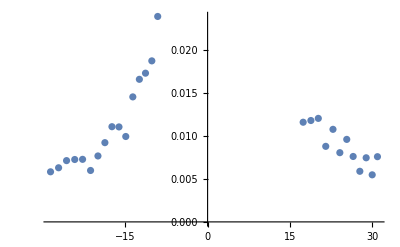

```mathematica
negativeCutoffs={4,29};
positiveCutoffs={16,35};
model=a/(δ)^2+b/(δ)^4+d;


temp=Dataset[positiveDetunings];
temp=temp[Select[Abs[#[[1]]]<positiveCutoffs[[2]]&]];
temp=temp[Select[Abs[#[[1]]]>positiveCutoffs[[1]]&]];
ListPlot[Normal[temp]]

nlmFit =NonlinearModelFit[Normal[temp],model(*,e>-10,e<10}*),{{a,1},{b,1},{d,0}},δ];
replacements=nlmFit["BestFitParameters"];

temp =Transpose[Normal[temp]];
temp[[2]]=temp[[2]]-d/.replacements;
positiveDetuningsZeroed=Transpose[{temp[[1]],temp[[2]]}];


temp=Dataset[negativeDetunings];
temp=temp[Select[Abs[#[[1]]]<negativeCutoffs[[2]]&]];
temp=temp[Select[Abs[#[[1]]]>negativeCutoffs[[1]]&]];
ListPlot[Normal[temp]]
(*
nlmFit =NonlinearModelFit[Normal[temp],model(*,e>-10,e<10}*),{{a,1},{b,1},{d,0}},δ];
replacements=nlmFit["BestFitParameters"];
*)

temp =Transpose[Normal[temp]];
temp[[2]]=temp[[2]]-d/.replacements;
negativeDetuningsZeroed=Transpose[{temp[[1]],temp[[2]]}];
allDataZeroed=Join[positiveDetuningsZeroed,negativeDetuningsZeroed];
ListPlot[allDataZeroed]
```

Fit Parameters for Number Density

Parameter Errors 1/δ^2+1/δ^4

Replacements Excluding δ^4

Parameter Errors 1/δ^2

Number Density (cm^-3):

1.4378×10^12

Number Density Error (cm^-3):

3.03783×10^11

Number Density Simple(cm^-3):

1.44169×10^12

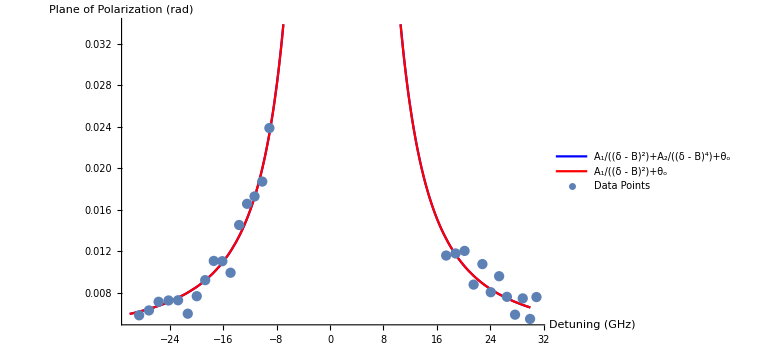

Fit Parameters for Number Density

Parameter Errors 1/δ^2+1/δ^4

Replacements Excluding δ^4

Parameter Errors 1/δ^2

Number Density (cm^-3):

1.67647×10^12

Number Density Error (cm^-3):

3.9845×10^11

Number Density Simple(cm^-3):

1.41977×10^12

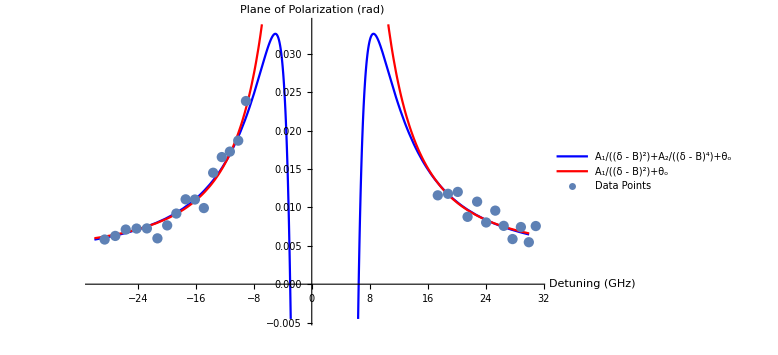

Fit Parameters for Number Density

Parameter Errors 1/δ^2+1/δ^4

Replacements Excluding δ^4

Parameter Errors 1/δ^2

Number Density (cm^-3):

2.84275×10^12

Number Density Error (cm^-3):

8.10831×10^11

Number Density Simple(cm^-3):

1.38718×10^12

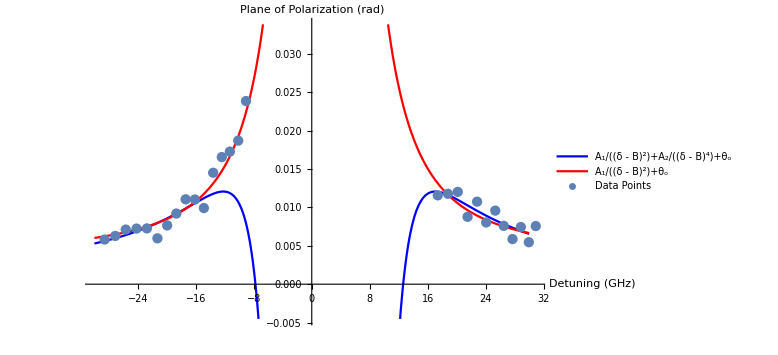

Fit Parameters for Number Density

Parameter Errors 1/δ^2+1/δ^4

Replacements Excluding δ^4

Parameter Errors 1/δ^2

Number Density (cm^-3):

3.44163×10^11

Number Density Error (cm^-3):

1.21418×10^12

Number Density Simple(cm^-3):

1.24169×10^12

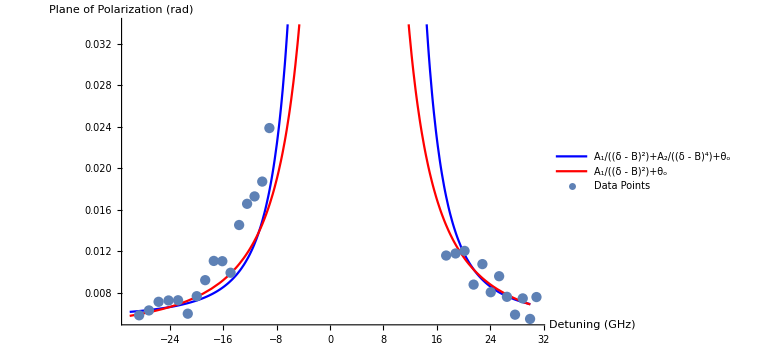

Fit Parameters for Number Density

Parameter Errors 1/δ^2+1/δ^4

Replacements Excluding δ^4

Parameter Errors 1/δ^2

Number Density (cm^-3):

-4.31638×10^13

Number Density Error (cm^-3):

1.90969×10^13

Number Density Simple(cm^-3):

2.54711×10^12

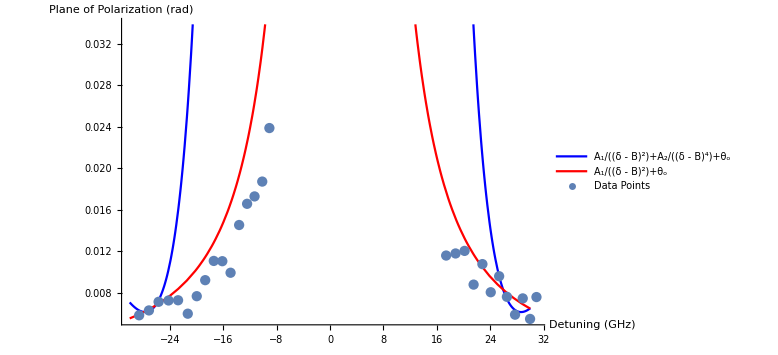

6.20151×10^11

```mathematica
(* Calculates fit for data *)
(* Removes datapoints that wrapped in rotation *)
For[low=5,low<26,low+=5,
lowerBoundDetuning=low;
upperBoundDetuning= 35;
dataset=Dataset[allDataZeroed];
dataset=dataset[Select[Abs[#[[1]]]<upperBoundDetuning&]];
dataset=dataset[Select[Abs[#[[1]]]>lowerBoundDetuning&]];
alldata = Normal[dataset];
labelSize=18;
color=Blue;
color2=LightOrange;

Clear[a,b,c,d,e];
$Assumptions=a>0;
$Assumptions=b>0;
dataset=Dataset[alldata];
maxmin=Dataset[allDataZeroed][MinMax,2];
ListPlot[Normal[dataset],PlotRange->All];
νo=377.107;
(*maxmin={datasetmm[-1][2],datasetmm[1][2]};*)
model=a/(δ-e)^2+b/(δ-e)^4+d;
(*model=a/(δ)^2+b/(δ)^4+d;*)
Print["Fit Parameters for Number Density"];
nlmFit =NonlinearModelFit[Normal[dataset],model(*,e>-10,e<10}*),{{a,1},{b,1},{d,0},{e,1}},δ];
(*nlmFit =NonlinearModelFit[Normal[dataset],model,{{a,1},{b,1},{d,0}},δ];*)
replacements=nlmFit["BestFitParameters"];
plot=Plot[Legended[Evaluate[model/.replacements],"A_1/(δ - B)^2+A_2/(δ - B)^4+θ_o"],{δ,30,-30},PlotRange->{Min[maxmin]-.01,Max[maxmin]+.01},PlotStyle->color,LabelStyle->labelSize];
(*plot=Plot[Legended[Evaluate[model/.replacements],"A_1/(δ)^2+A_2/(δ)^4+θ_o"],{δ,30,-30},PlotRange->{Min[maxmin]-.01,Max[maxmin]+.01},PlotStyle->color,LabelStyle->labelSize];
modelf=Function[{δ},Evaluate[model/.replacements]];*)
Print["Parameter Errors 1/δ^2+1/δ^4"];
errors=nlmFit["ParameterErrors"];
(*errorList={(a/.replacements) +errors[[1]],(b/.replacements)+errors[[2]],(d/.replacements)+errors[[3]],(e/.replacements)+errors[[4]]};
plotPlusError=Plot[errorList[[1]]/(δ)^2+errorList[[2]]/(δ)^4+errorList[[3]],{δ,30,-30},PlotRange->{Min[maxmin]-.01,Max[maxmin]+.01},PlotStyle->color2,LabelStyle->labelSize];
errorList={(a/.replacements) -errors[[1]],(b/.replacements)-errors[[2]],(d/.replacements)-errors[[3]],(e/.replacements)-errors[[4]]};
plotMinusError=Plot[Legended[errorList[[1]]/(δ)^2+errorList[[2]]/(δ)^4+errorList[[3]],"A_1/(δ - B)^2+A_2/(δ - B)^4+θ_o (Error)"],{δ,30,-30},PlotRange->{Min[maxmin]-.01,Max[maxmin]+.01},PlotStyle->color2,LabelStyle->labelSize];*)
{δl,θl}=Transpose[Normal[dataset]];
Map[modelf,δl];


modelNo4=a/(δ-e)^2+d;
(*modelNo4=a/(δ)^2+d;*)
Print["Replacements Excluding δ^4"];
nlmFit2=NonlinearModelFit[Normal[dataset],modelNo4,{{a,4},{d,-1},{e,1}},δ,AccuracyGoal->5];
(*nlmFit2=NonlinearModelFit[Normal[dataset],modelNo4,{{a,4},{d,-1}},δ,AccuracyGoal->5];*)
replacementsNo4=nlmFit2["BestFitParameters"];
plotNo4=Plot[Legended[Evaluate[modelNo4/.replacementsNo4],"A_1/(δ - B)^2+θ_o"],{δ,30,-30},PlotRange->{Min[maxmin]-.01,Max[maxmin]+.01},PlotStyle->Red,LabelStyle->labelSize];
(*plotNo4=Plot[Legended[Evaluate[modelNo4/.replacementsNo4],"A_1/(δ)^2+θ_o"],{δ,30,-30},PlotRange->{Min[maxmin]-.01,Max[maxmin]+.01},PlotStyle->Red,LabelStyle->labelSize];*)
modelfNo4=Function[{δ},Evaluate[modelNo4/.replacementsNo4]];
{δl,θl}=Transpose[Normal[dataset]];
Print["Parameter Errors 1/δ^2"];
errorsNo4=nlmFit2["ParameterErrors"];
(*errorList={(a/.replacements) +errorsNo4[[1]],(d/.replacements)+errorsNo4[[2]],(e/.replacements) +errorsNo4[[3]]};
plotNo4PlusError=Plot[errorList[[1]]/(δ-errorList[[3]])^2+errorList[[2]],{δ,30,-30},PlotRange->{Min[maxmin]-.01,Max[maxmin]+.01},PlotStyle->LightRed,LabelStyle->labelSize];
errorList={(a/.replacements) -errorsNo4[[1]],(d/.replacements)-errorsNo4[[2]],(e/.replacements) -errorsNo4[[3]]};
plotNo4MinusError=Plot[Legended[errorList[[1]]/(δ-errorList[[3]])^2+errorList[[2]],"A_1/(δ - B)^2+θ_o (Error)"],{δ,30,-30},PlotRange->{Min[maxmin]-.01,Max[maxmin]+.01},PlotStyle->LightRed,LabelStyle->labelSize];*)


linearRotationFit=LinearModelFit[Normal[dataset],x,x];

c=2.99792458*^8;
re=2.8179*^-15;
fge=0.34231;
k=4/3;
BdotL;
μ=9.2740*^-24;
h=6.6261*^-34;
ν0=377107.463;
conversionFactor=h/(BdotL*c*re*fge*k*μ)*10^18*10^-6;(*Conversion Factor is in 1/(Hz)^2, so we need *10^18 to convert to 1/(GHz)^2*)

Print["Number Density (cm^-3):"];
n=(a/.replacements)* conversionFactor;
Print[n];
errors=nlmFit["ParameterErrors"];
Print["Number Density Error (cm^-3):"];
nErr=errors[[1]]*conversionFactor;
Print[nErr];

Print["Number Density Simple(cm^-3):"];
nNo4 =(a/.replacementsNo4)*conversionFactor;
Print[nNo4];
finalResult=Show[plot,plotNo4,ListPlot[Legended[allDataZeroed,"Data Points"],LabelStyle->labelSize],AxesLabel->{"Detuning\n(GHz)","Plane of Polarization (rad)"},ImageSize->Large,PlotRange->All];
Print[finalResult];
fitList={{"theta_0","A_1","B","theta_0'","A_1'","B'","A_2'"},
{d/.replacementsNo4,a/.replacementsNo4,e/.replacementsNo4,d/.replacements,a/.replacements,e/.replacements,b/.replacements},
{errorsNo4[[2]],errorsNo4[[1]],errorsNo4[[3]],errors[[3]],errors[[1]],errors[[4]],errors[[2]]}};
(*fitList={{"theta_0","A_1","theta_0'","A_1'","A_2'"},
{d/.replacementsNo4,a/.replacementsNo4,d/.replacements,a/.replacements,b/.replacements},
{errorsNo4[[2]],errorsNo4[[1]],errors[[3]],errors[[1]],errors[[2]]}};*)
Export["fitStatistics_DetuningCutoff"<>ToString[low]<>".tsv",fitList];
Export["fitGraph_DetuningCutoff"<>ToString[low]<>".png",finalResult];
]
Print[conversionFactor];
```

```mathematica
allDetunings=Join[positiveDetunings,negativeDetunings]
```

{{27.5546,-1.09804},{26.5566,-1.09836},{25.3941,-1.09965},{24.2595,-1.09956},{23.1005,-1.09903},{21.919,-1.10297},{20.6869,-1.09836},{19.4373,-1.09643},{18.1392,-1.09957},{16.8401,-1.09739},{15.4888,-1.09614},{14.136,-1.09708},{12.7503,-1.09637},{11.3771,-1.09814},{9.96648,-1.09634},{8.52416,-1.09051},{7.01173,-1.09431},{5.50793,-1.0898},{4.04704,-1.08996},{2.50836,-1.08917},{-13.4495,-1.07598},{-14.4384,-1.07414},{-15.5302,-1.07614},{-16.6886,-1.0762},{-17.8381,-1.07386},{-19.0317,-1.07299},{-20.2809,-1.07233},{-21.5334,-1.07046},{-22.8002,-1.07182},{-24.0455,-1.07005},{-25.3375,-1.06963},{-26.6933,-1.07004},{-28.0757,-1.06622},{-29.4581,-1.06604},{-30.894,-1.0651},{-32.3246,-1.06452},{-33.7798,-1.06496},{-35.2126,-1.06469},{-36.7411,-1.06564},{-38.3379,-1.06218}}

```mathematica
lm=LinearModelFit[allDetunings,x,x]
```

FittedModel[-1.08596-0.000631806 x]